```mathematica
myFileNames = FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/20190226_fixed_TL_cy3_accum_15h/TL*"];
```

```mathematica
myFiles = Import/@myFileNames;
```

```mathematica
ImageAdjust/@myFiles[[1]]
```

{-Graphics-,-Graphics-}

```mathematica
ImageResize[-Graphics-,{64,64}]
```

-Graphics-

```mathematica
ImageAdjust@myFiles[[1,1]]
```

-Graphics-

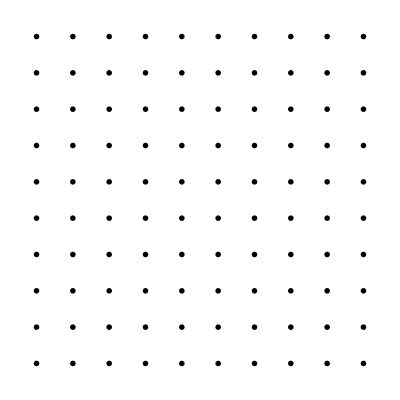

```mathematica
myCellsG = Table[ImageResize[ImageAdjust[myFiles[[img,1]],{1,1,1},{.0001,.15}],{64,64}],{img,1,101,1}];
GraphicsGrid[Partition[myCellsG,10]]
```

```mathematica
myCellsG = Table[ImageResize[ImageAdjust@myFiles[[img,1]],{64,64}],{img,1,101,1}];
gridG=GraphicsGrid[Partition[myCellsG,10]]
```

-Graphics-

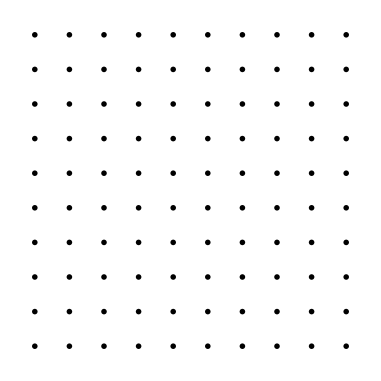

```mathematica
myCellsB = Table[ImageResize[
ImageAdjust[myFiles[[img,2]],{1,1,1},{.00001,.075}],{64,64}],{img,1,100,1}];
gridB=GraphicsGrid[Partition[myCellsB,10]]
```

```mathematica
dummyImg = Flatten[Table[Flatten@Table[0,1,64],1,64],1]//Image
dummyImgW = Flatten[Table[Flatten@Table[1,1,64],1,64],1]//Image
dummyImg//ImageDimensions
```

-Graphics-

-Graphics-

{64,64}

```mathematica
dummyImgs =GraphicsGrid[  Partition[Table[-Graphics-,100],10]  ]
```

-Graphics-

```mathematica
ColorNegate[(myCellsG[[1]]+ myCellsB[[1]])/.5]
```

-Graphics-

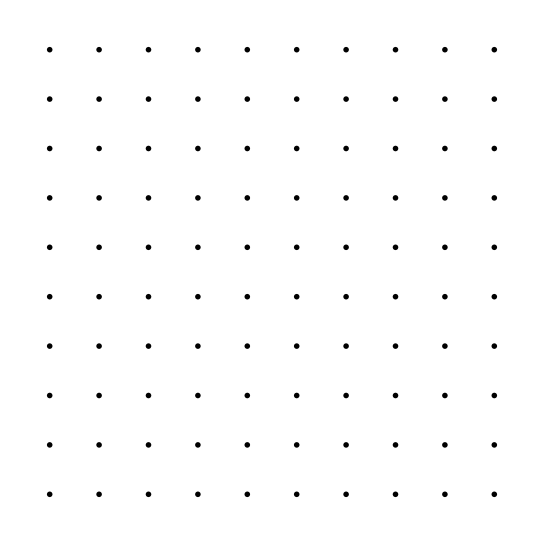

```mathematica
GraphicsGrid[Partition[ Table[ColorCombine[{myCellsB[[i]], myCellsG[[i]], dummyImg,ColorNegate[(myCellsG[[i]]+ myCellsB[[i]])/2]},"CMYK"],  {i,1,100}],10]]
```

```mathematica
myTable = ColorCombine[{dummyImgs,gridG,gridB}]
```

-Graphics-

```mathematica
Export["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/20190226_fixed_TL_cy3_accum_15h/TL100table.png",myTable]
```

/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/20190226_fixed_TL_cy3_accum_15h/TL100table.png